```mathematica
ChromaticPolynomial[ReadGraph[8,1],4]
```

24

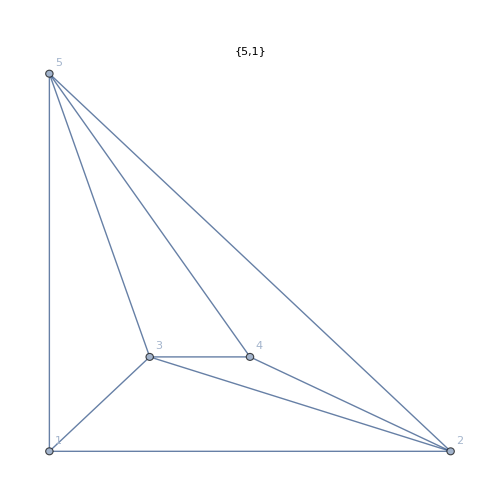
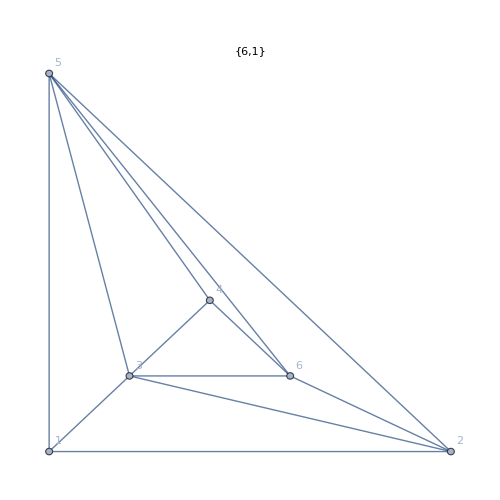
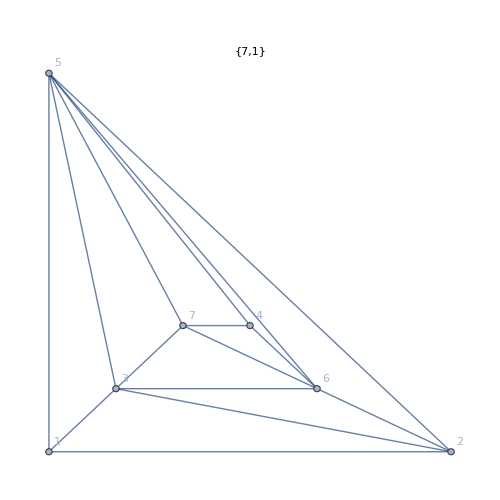
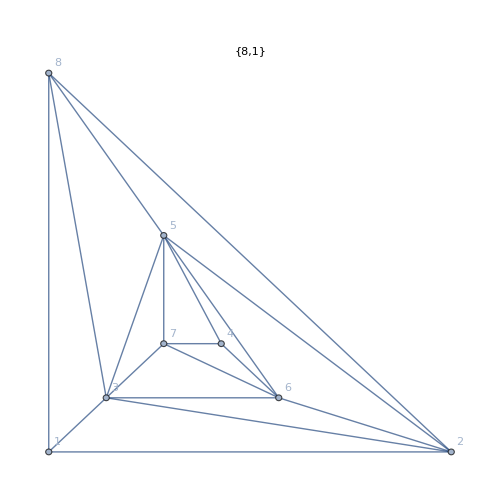
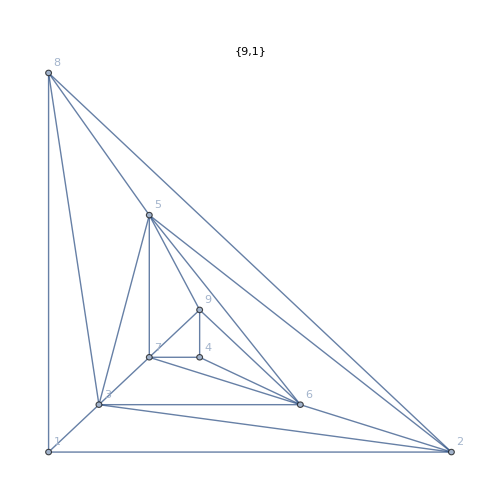
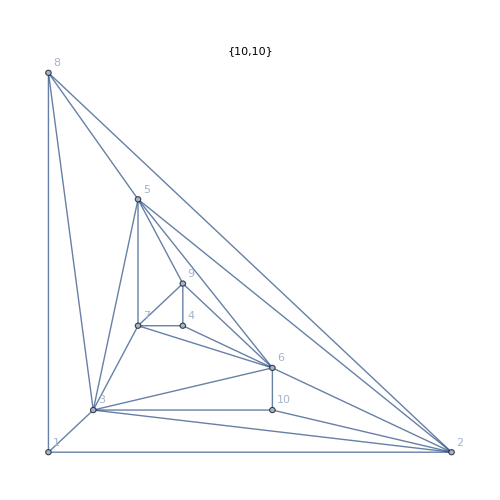
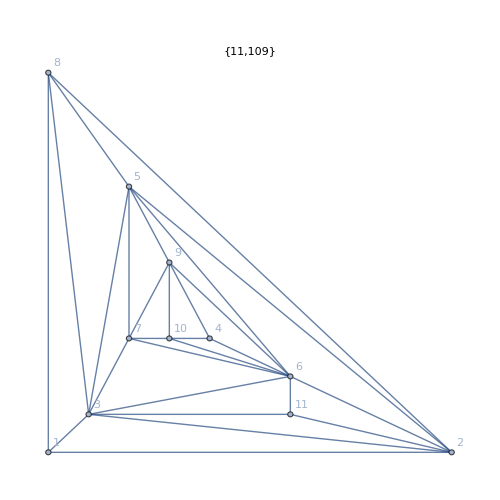
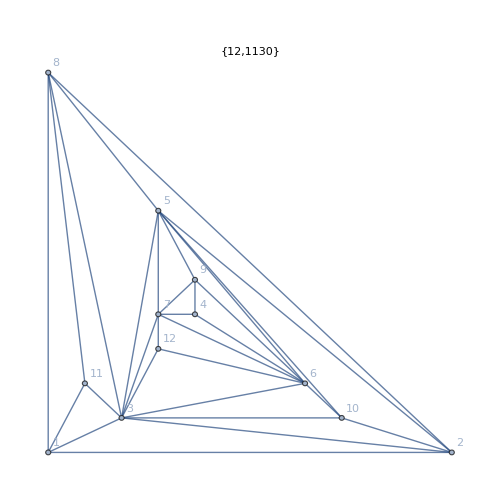
{{-Graphics-,24,264},{-Graphics-,24,1752},{-Graphics-,24,11784},{-Graphics-,24,18456},{-Graphics-,24,119976},{-Graphics-,24,87216},{-Graphics-,24,60720},{-Graphics-,24,147144},{-Graphics-,24,696480},{-Graphics-,24,5224536}}

```mathematica
Map[With[{g=Graph[ReadGraph[#[[1]],#[[2]]],GraphLayout->"PlanarEmbedding", VertexLabels->"Name", ImageSize->500,PlotLabel->{#[[1]],#[[2]]}]},{g, ChromaticPolynomial[g,4], ChromaticPolynomial[DualGraph[Faces[g]],4]}]&,{{5,1},{6,1},{7,1},{8,1},{9,1},{10,10},{11,109},{12,1130},{13,11293},{14,119676}}]
```

```mathematica
Map[With[{g=Graph[ReadGraph[#[[1]],#[[2]]],GraphLayout->"PlanarEmbedding", VertexLabels->"Name", ImageSize->500,PlotLabel->{#[[1]],#[[2]]}]},{g, ChromaticPolynomial[g,4], ChromaticPolynomial[DualGraph[Faces[g]],4]}]&,{{5,1},{6,1},{7,1},{8,1},{9,1},{10,10},{11,109},{12,1130},{13,11293},{14,119676}}]
```

```mathematica
ChromaticPolynomial[CompleteGraph[4],4]
```

24